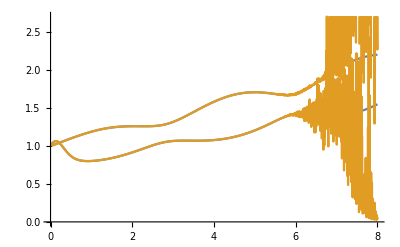

```mathematica
Clear[f,df,p,a,b,c,y,J,M]
SetOptions[SingularValueList,Tolerance->0];f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y, b+z(x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:={{0,-1,-1},{1,a,0},{z, 0,-c}}
p={a,b,c}={0.2,0.2,5.7};
y0={3,3,6}; TMax=8;
Id=IdentityMatrix[3];
{ySol,JSol,MSol}=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
M'[t]==-df[p][y[t]]ᵀ.M[t],
y[0]==y0, J[0]==Id,M[0]==Id
},{y,J,M},{t,0, TMax}];
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All];
LogPlot[ {
SingularValueList[JSol[t]],
1/SingularValueList[MSol[t]]
},{t,0, TMax}];
Plot[ {
SingularValueList[JSol[t]]⟦{1,2}⟧,
1/SingularValueList[MSol[t]]⟦{2,3}⟧
},{t,0, TMax}]
```

```mathematica
ClearAll[f,df,LTSk,Dia]
f[{x_,y_,z_}]:={-y-z,x+0.2 y,0.2+z (x-5.7)}
df[{x_,y_,z_}]:={{0,-1,-1},{1,0.2,0},{z,0,x-5.7}};
LTSk[M_?MatrixQ]:=Module[{L=LowerTriangularize[M,-1]},
L-Lᵀ] 
Dia[M_?MatrixQ]:=Diagonal[M]

y0={1,2,3}; Id=IdentityMatrix[Length[y0]];
TMax=23;

{ySol,JSol,QSol,rSol}=NDSolveValue[{
y'[t]==f[y[t]],
J'[t]==df[y[t]].J[t],
Q'[t]==Q[t].LTSk[Q[t]ᵀ.df[y[t]].Q[t]],
r'[t]==Dia[Q[t]ᵀ.df[y[t]].Q[t]]*r[t],
y[0]==y0,
J[0]==Id,
Q[0]==Id,
r[0]=={1,1,1}
},{y,J,Q,r},{t,0,TMax}];
TabView[{
"r"->LogPlot[rSol[t],{t,0,TMax},PlotRange->{10^-32,10}],
"σ"->LogPlot[SingularValueList[JSol[t],Tolerance->0],{t,0,TMax},PlotRange->{10^-32,10}],
"orth"->LogPlot[Norm[QSol[t]ᵀ.QSol[t]-Id],{t,0, TMax}]
}]
```

```mathematica
{QT,RT}=QRDecomposition[QSol[TMax]];
MatrixForm[RT]
```